```mathematica
(* Paul Popa *)
(* PS5 *)

(* Exercise 1 *)
```

```mathematica
f[x_] := x*Exp[-x]-1;
```

```mathematica
df[x_]=D[f[x],x];
```

```mathematica
df2[x_]=D[df[x],x];
```

```mathematica
df3[x_]=D[df2[x],x];
```

```mathematica
g[x_] := f[2.5]+df[2.5]*(x-2.5)+(1/2!)*df2[2.5]*(x-2.5)^2+(1/3!)*df3[2.5]*(x-2.5)^3
```

```mathematica
g[x]
```

-0.794788-0.123127 (-2.5+x)+0.0205212 (-2.5+x)^2+0.00684042 (-2.5+x)^3

```mathematica
normErr=(NIntegrate[(f[x]-g[x])^2,{x,1,4}])^(1/2)
```

0.0187681

```mathematica
meanNormErr=normErr/(4-1)
```

0.00625605

```mathematica
(* Exercise 2 *)
```

```mathematica
(* a *)
```

```mathematica
x1=1;
y1=f[x1];
```

```mathematica
x2=2;
y2=f[x2];
```

```mathematica
x3=3;
y3=f[x3];
```

```mathematica
x4=4;
y4=f[x4];
```

```mathematica
n=3;
```

```mathematica
xMat={{1,x1,x1^2,x1^3},{1,x2,x2^2,x2^3},{1,x3,x3^2,x3^3},{1,x4,x4^2,x4^3}};
```

```mathematica
yMat={y1,y2,y3,y4};
```

```mathematica
MatrixForm[xMat]
```

(1 | 1 | 1 | 1
1 | 2 | 4 | 8
1 | 3 | 9 | 27
1 | 4 | 16 | 64)

```mathematica
MatrixForm[yMat]
```

(-1+1/ⅇ
-1+2/ⅇ^2
-1+3/ⅇ^3
-1+4/ⅇ^4)

```mathematica
coeffMat=LinearSolve[xMat,yMat]
```

{(-4+12 ⅇ-12 ⅇ^2+4 ⅇ^3-ⅇ^4)/ⅇ^4,(22-63 ⅇ+57 ⅇ^2-13 ⅇ^3)/(3 ⅇ^4),(-8+21 ⅇ-16 ⅇ^2+3 ⅇ^3)/(2 ⅇ^4),(4-9 ⅇ+6 ⅇ^2-ⅇ^3)/(6 ⅇ^4)}

```mathematica
(* b *)
```

```mathematica
p=coeffMat[[1]]+coeffMat[[2]]*x+coeffMat[[3]]*x^2+coeffMat[[4]]*x^3
```

(-4+12 ⅇ-12 ⅇ^2+4 ⅇ^3-ⅇ^4)/ⅇ^4+((22-63 ⅇ+57 ⅇ^2-13 ⅇ^3) x)/(3 ⅇ^4)+((-8+21 ⅇ-16 ⅇ^2+3 ⅇ^3) x^2)/(2 ⅇ^4)+((4-9 ⅇ+6 ⅇ^2-ⅇ^3) x^3)/(6 ⅇ^4)

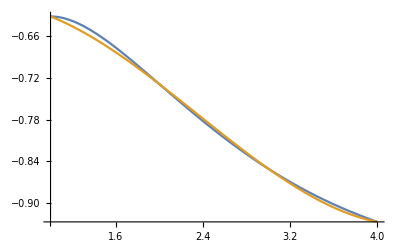

```mathematica
Plot[{f[x],p},{x,1,4}]
```

```mathematica
(* c *)
```

```mathematica
normErrPoly=(NIntegrate[(f[x]-p)^2,{x,1,4}])^(1/2)
```

0.00748051

```mathematica
meanNormErrPoly=normErrPoly/(4-1)
```

0.0024935

```mathematica
(* d *)
```

```mathematica
fTaylorErr = f[x]-g[x]
```

-0.205212+0.123127 (-2.5+x)-0.0205212 (-2.5+x)^2-0.00684042 (-2.5+x)^3+ⅇ^-x x

```mathematica
fTaylorErr/.x->2.5
```

-5.55112×10^-17

```mathematica
fpErr=f[x]-p
```

-1-(-4+12 ⅇ-12 ⅇ^2+4 ⅇ^3-ⅇ^4)/ⅇ^4+ⅇ^-x x-((22-63 ⅇ+57 ⅇ^2-13 ⅇ^3) x)/(3 ⅇ^4)-((-8+21 ⅇ-16 ⅇ^2+3 ⅇ^3) x^2)/(2 ⅇ^4)-((4-9 ⅇ+6 ⅇ^2-ⅇ^3) x^3)/(6 ⅇ^4)

```mathematica
fpErr/.x->2.5
```

-0.003484

```mathematica
(* p is a worse approximation than the cubic Taylor interpolation as the error functions for each display above; the error with f(x) and the cubic Taylor interpolation is closer to 0 than that of f(x) and p(x). *)
```

```mathematica
(* e *)
```

```mathematica
maxErr=D[f[x],{x,5}]/4!*(4-1)^3
```

9/8 (5 ⅇ^-x-ⅇ^-x x)

```mathematica
maxErr/.x->4
```

9/(8 ⅇ^4)

```mathematica
N[9/(8 ⅇ^4),7]
```

0.02060509

```mathematica
(* Exercise 3 *)
```

```mathematica
(* Redefine x as z and f(x) as h(z) *)
```

```mathematica
h[z_]:=1/(1+z^2);
```

```mathematica
h[z]
```

1/(1+z^2)

```mathematica
z1=-2;
h1=h[z1];
```

```mathematica
z2=-1;
h2=h[z2];
```

```mathematica
z3=0;
h3=h[z3];
```

```mathematica
z4=1;
h4=h[z4];
```

```mathematica
z5=2;
h5=h[z5];
```

```mathematica
n=4;
```

```mathematica
zMat={{1,z1,z1^2,z1^3,z1^4},{1,z2,z2^2,z2^3,z2^4},{1,z3,z3^2,z3^3,z3^4},{1,z4,z4^2,z4^3,z4^4},{1,z5,z5^2,z5^3,z5^4}};
```

```mathematica
hMat={z1,z2,z3,z4,z5};
```

```mathematica
MatrixForm[zMat]
```

(1 | -2 | 4 | -8 | 16
1 | -1 | 1 | -1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16)

```mathematica
MatrixForm[hMat]
```

(-2
-1
0
1
2)

```mathematica
LinearSolve[zMat,hMat]
```

{0,1,0,0,0}

```mathematica
p3=x;
```

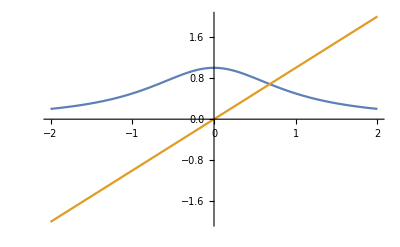

```mathematica
Plot[{h[x],p3},{x,-2,2}]
```

```mathematica
normErrPoly2=(NIntegrate[(f[x]-p3)^2,{x,-2,2}])^(1/2)
```

8.14015

```mathematica
meanNormErrPoly2=normErrPoly2/(2-(-2))
```

2.03504

```mathematica
(* Extra Credit *)
```

```mathematica
(* The equation to be utilized is based on the time it takes for a binary star system to merge. *)
```

```mathematica
c=3.0*10^8; (* speed of light *)
```

```mathematica
G=6.67*10^-11; (* Gravitational constant *)
```

```mathematica
m1=1.6*10^31; (* mass of first white dwarf *)
```

```mathematica
m2=1.0*10^31; (* mass of second white dwarf *)
```

```mathematica
r[x_]=(5/256)*(c^5/G^3)*((x^4)/(m1*m2*(m1+m2)));
```

```mathematica
D[r[x],{x,2}]
```

4.61367×10^-22 x^2

```mathematica
D[r[x],{x,3}]
```

9.22734×10^-22 x

```mathematica
r1=1.1;
r2=1.3;
r3=1.5;
r4=1.7;
r5=1.9;
r6=2.1;
r7=2.3;
r8=2.5;
r9=2.7;
r10=2.9;
(* Assume each radius is multiplied by 10^9 *)
```

```mathematica
rArray={r1,r2,r3,r4,r5,r6,r7,r8,r9,r10};
```

```mathematica
rSol1=r[r1];
rSol2=r[r2];
rSol3=r[r3];
rSol4=r[r4];
rSol5=r[r5];
rSol6=r[r6];
rSol7=r[r7];
rSol8=r[r8];
rSol9=r[r9];
rSol10=r[r10];
```

```mathematica
n=9;
```

```mathematica
rMat={{1,r1,r1^2,r1^3,r1^4,r1^5,r1^6,r1^7,r1^8,r1^9},{1,r2,r2^2,r2^3,r2^4,r2^5,r2^6,r2^7,r2^8,r2^9},{1,r3,r3^2,r3^3,r3^4,r3^5,r3^6,r3^7,r3^8,r3^9},{1,r4,r4^2,r4^3,r4^4,r4^5,r4^6,r4^7,r4^8,r4^9},{1,r5,r5^2,r5^3,r5^4,r5^5,r5^6,r5^7,r5^8,r5^9},{1,r6,r6^2,r6^3,r6^4,r6^5,r6^6,r6^7,r6^8,r6^9},{1,r7,r7^2,r7^3,r7^4,r7^5,r7^6,r7^7,r7^8,r7^9},{1,r8,r8^2,r8^3,r8^4,r8^5,r8^6,r8^7,r8^8,r8^9},{1,r9,r9^2,r9^3,r9^4,r9^5,r9^6,r9^7,r9^8,r9^9},{1,r10,r10^2,r10^3,r10^4,r10^5,r10^6,r10^7,r10^8,r10^9}};
```

```mathematica
MatrixForm[rMat]
```

(1 | 1.1 | 1.21 | 1.331 | 1.4641 | 1.61051 | 1.77156 | 1.94872 | 2.14359 | 2.35795
1 | 1.3 | 1.69 | 2.197 | 2.8561 | 3.71293 | 4.82681 | 6.27485 | 8.15731 | 10.6045
1 | 1.5 | 2.25 | 3.375 | 5.0625 | 7.59375 | 11.3906 | 17.0859 | 25.6289 | 38.4434
1 | 1.7 | 2.89 | 4.913 | 8.3521 | 14.1986 | 24.1376 | 41.0339 | 69.7576 | 118.588
1 | 1.9 | 3.61 | 6.859 | 13.0321 | 24.761 | 47.0459 | 89.3872 | 169.836 | 322.688
1 | 2.1 | 4.41 | 9.261 | 19.4481 | 40.841 | 85.7661 | 180.109 | 378.229 | 794.28
1 | 2.3 | 5.29 | 12.167 | 27.9841 | 64.3634 | 148.036 | 340.483 | 783.11 | 1801.15
1 | 2.5 | 6.25 | 15.625 | 39.0625 | 97.6563 | 244.141 | 610.352 | 1525.88 | 3814.7
1 | 2.7 | 7.29 | 19.683 | 53.1441 | 143.489 | 387.42 | 1046.04 | 2824.3 | 7625.6
1 | 2.9 | 8.41 | 24.389 | 70.7281 | 205.111 | 594.823 | 1724.99 | 5002.46 | 14507.1)

```mathematica
rSolMat={rSol1,rSol2,rSol3,rSol4,rSol5,rSol6,rSol7,rSol8,rSol9,rSol10};
```

```mathematica
MatrixForm[rSolMat]
```

(5.62906×10^-23
1.09809×10^-22
1.94639×10^-22
3.21115×10^-22
5.01049×10^-22
7.47726×10^-22
1.07591×10^-21
1.50185×10^-21
2.04325×10^-21
2.7193×10^-21)

```mathematica
MatSol=LinearSolve[rMat,rSolMat]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,1.1,1.21,1.331,1.4641,1.61051,1.77156,1.94872,2.14359,2.35795},«8»,{1.,2.9,8.41,24.389,70.7281,205.111,594.823,1724.99,5002.46,14507.1}} may contain significant numerical errors.

{1.70242×10^-33,-8.79105×10^-33,1.99823×10^-32,-2.6248×10^-32,3.84473×10^-23,-1.2135×10^-32,4.42804×10^-33,-1.02858×10^-33,1.37967×10^-34,-8.13897×10^-36}

```mathematica
LinearAlgebra`MatrixConditionNumber[rMat]
```

2.76552×10^11

```mathematica
(* Large condition number, so values may be incorrect, but will utilize in calculations *)
```

```mathematica
pEC[r_]:=1.702416063455001*^-33-8.791050780046447*^-33*r+1.9982289752152863*^-32*r^2-2.624800927994791*^-32*r^3+3.8447267603048406*^-23*r^4-1.2134951343098089*^-32*r^5+4.4280444163910356*^-33*r^6-1.028582491733672*^-33*r^7+1.379666236646309*^-34*r^8-8.138970403833775*^-36*r^9
```

```mathematica
pEC[x]
```

1.70242×10^-33-8.79105×10^-33 x+1.99823×10^-32 x^2-2.6248×10^-32 x^3+3.84473×10^-23 x^4-1.2135×10^-32 x^5+4.42804×10^-33 x^6-1.02858×10^-33 x^7+1.37967×10^-34 x^8-8.13897×10^-36 x^9

```mathematica
normErrPolyEC=(NIntegrate[(r[x]-pEC[x])^2,{x,1.1,2.9}])^(1/2)
```

1.44651×10^-37

```mathematica
meanNormErrPolyEC=normErrPolyEC/(2.9-1.1)
```

8.03619×10^-38

```mathematica
dr[x_]:=D[r[x],x]
```

```mathematica
dr[x]
```

1.53789×10^-22 x^3

```mathematica
dpEC[x_]:=D[pEC[x],x]
```

```mathematica
dpEC[x]
```

-8.79105×10^-33+3.99646×10^-32 x-7.8744×10^-32 x^2+1.53789×10^-22 x^3-6.06748×10^-32 x^4+2.65683×10^-32 x^5-7.20008×10^-33 x^6+1.10373×10^-33 x^7-7.32507×10^-35 x^8

```mathematica
normErrPolydpEC=(NIntegrate[(dr[x]-dpEC[x])^2,{x,1.1,2.9}])^(1/2)
```

1.63847×10^-36

```mathematica
meanNormErrPolydpEC=normErrPolydpEC/(2.9-1.1)
```

9.10258×10^-37

```mathematica
d2r[x_]:=D[dr[x],x]
```

```mathematica
d2r[x]
```

4.61367×10^-22 x^2

```mathematica
d2pEC[x_]:=D[dpEC[x],x]
```

```mathematica
d2pEC[x]
```

3.99646×10^-32-1.57488×10^-31 x+4.61367×10^-22 x^2-2.42699×10^-31 x^3+1.32841×10^-31 x^4-4.32005×10^-32 x^5+7.72613×10^-33 x^6-5.86006×10^-34 x^7

```mathematica
normErrPolyd2pEC=(NIntegrate[(d2r[x]-d2pEC[x])^2,{x,1.1,2.9}])^(1/2)
```

3.40439×10^-35

```mathematica
meanNormErrPolyd2pEC=normErrPolyd2pEC/(2.9-1.1)
```

1.89133×10^-35

```mathematica
(* Comparing error of r(x) and pEC(x) *)
```

```mathematica
r[1.1]
```

5.62906×10^-23

```mathematica
NumberForm[5.629064446547114*^-23,20]
```

5.629064446547114×10^-23

```mathematica
pEC[1.1]
```

5.62906×10^-23

```mathematica
NumberForm[5.629064446547114*^-23,20]
```

5.629064446547114×10^-23

```mathematica
e1=r[x]-pEC[x]
```

-1.70242×10^-33+8.79105×10^-33 x-1.99823×10^-32 x^2+2.6248×10^-32 x^3-2.19603×10^-32 x^4+1.2135×10^-32 x^5-4.42804×10^-33 x^6+1.02858×10^-33 x^7-1.37967×10^-34 x^8+8.13897×10^-36 x^9

```mathematica
e1/.x->1.1
```

-2.61871×10^-39

```mathematica
(* Comparing error of dr(x) and dpEC(x) *)
```

```mathematica
dr[x]/.x->1.1
```

2.04693×10^-22

```mathematica
NumberForm[2.0469325260171324*^-22,20]
```

2.046932526017132×10^-22

```mathematica
dpEC[x]/.x->1.1
```

2.04693×10^-22

```mathematica
NumberForm[2.046932526017125*^-22,20]
```

2.046932526017125×10^-22

```mathematica
e2=dr[x]-dpEC[x]
```

8.79105×10^-33-3.99646×10^-32 x+7.8744×10^-32 x^2-8.78411×10^-32 x^3+6.06748×10^-32 x^4-2.65683×10^-32 x^5+7.20008×10^-33 x^6-1.10373×10^-33 x^7+7.32507×10^-35 x^8

```mathematica
e2/.x->1.1
```

7.42103×10^-37

```mathematica
(* Comparing error of d2r(x) and d2pEC(x) *)
```

```mathematica
d2r[x]/.x->1.1
```

5.58254×10^-22

```mathematica
NumberForm[5.582543252773997*^-22,20]
```

5.582543252773997×10^-22

```mathematica
d2pEC[x]/.x->1.1
```

5.58254×10^-22

```mathematica
NumberForm[5.582543252774217*^-22,20]
```

5.582543252774217×10^-22

```mathematica
e3=d2r[x]-d2pEC[x]
```

-3.99646×10^-32+1.57488×10^-31 x-2.63523×10^-31 x^2+2.42699×10^-31 x^3-1.32841×10^-31 x^4+4.32005×10^-32 x^5-7.72613×10^-33 x^6+5.86006×10^-34 x^7

```mathematica
e3/.x->1.1
```

-2.203×10^-35

```mathematica
(* The error of r(x) and pEC(x) can be considered equal to each other as far as Mathematica is concerned as the number of digits after the decimal place can be expanded only as much as shown above and, up to that limit, the two numbers are equal.

The error of dr(x) and dpEC(x) differ slightly beginning 14 places after the decimal point. The derivative of the interpolation has a smaller error than that of the function.

The error of d2r(x) and d2pEC(x) differ slightly beginning 12 places after the decimal point. The derivative of the interpolation has a smaller error than that of the function.

It is not possible to calculte the maximum error on r(x) as there are not 
n+1 continuous derivatives, only 4 continuous derivatives. If it were possible to calculate the max error, one would simply take the value of n (which is 9 in this case as there are n+1 = 10 points) along with the value of x equal to max([a,b]) within some interval [a,b] defined on the function and solve for |e(x)| ≤ |f^10(2.9)|/10! * (2.9-1.1)^10 where n=9, a=1.1, and b=2.9, and x=2.9 as this is the max value in our interval from 1.1 to 2.9 *)
```

```mathematica
(* Solving using the Lagrange *)
```

```mathematica
l1=With[{j=1,n=10},Product[(x-rArray[[i]])/(-rArray[[i]]+rArray[[j]]),{i,Complement[Range[1,n],{j}]}]];
l1=l1*rSol1;
For[m=2,m≤10,m++,
l=With[{j=m,n=10},Product[(x-rArray[[i]])/(-rArray[[i]]+rArray[[j]]),{i,Complement[Range[1,n],{j}]}]];
l1=l1+l*rSolMat[[j]];
];
```

```mathematica
l1
```

-3.02973×10^-22 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x)+1.5555×10^-20 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.1+x)-6.22201×10^-20 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.3+x) (-1.1+x)+1.4518×10^-19 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.5+x) (-1.3+x) (-1.1+x)-2.1777×10^-19 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)+2.1777×10^-19 (-2.9+x) (-2.7+x) (-2.5+x) (-2.3+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)-1.4518×10^-19 (-2.9+x) (-2.7+x) (-2.5+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)+6.22201×10^-20 (-2.9+x) (-2.7+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)-1.5555×10^-20 (-2.9+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)+1.72834×10^-21 (-2.7+x) (-2.5+x) (-2.3+x) (-2.1+x) (-1.9+x) (-1.7+x) (-1.5+x) (-1.3+x) (-1.1+x)

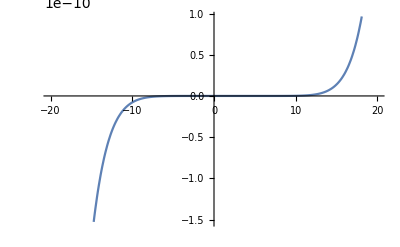

```mathematica
Plot[l1,{x,-20,20}]
```